```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Initial Params*)
Directory[]
```

/home/sarah/transients-simulations

```mathematica
params = Import["./python36/config.ini","Ini"]
```

<|INITIAL PARAMETERS→<|n_sources → 2e6  ,fl_min → 5e-5   ,fl_max → 5   ,flux_err → 1e-1  ,dmin → 5e-3 ,dmax → 5e3    ,det_threshold → 5 ,extra_threshold → 3  ,file → output   ,lightcurvetype → gaussian |>,SIM→<|nobs → 46 ,obssens → 31.7e-6 ,obssig → 4.6e-6 ,obsinterval → 7,obsdurations → 0.009 |>|>

```mathematica
startexec = DateObject[];
nsources = ToExpression[StringReplace[params[[1]][[1]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
fluxmin =ToExpression[StringReplace[params[[1]][[2]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
fluxmax =ToExpression[StringReplace[params[[1]][[3]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
fluxerr =ToExpression[StringReplace[params[[1]][[4]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
dmin =ToExpression[StringReplace[params[[1]][[5]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
dmax = ToExpression[StringReplace[params[[1]][[6]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
detThreshold = ToExpression[StringReplace[params[[1]][[7]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
extraThreshold =ToExpression[StringReplace[params[[1]][[8]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
file = StringDelete[params[[1]][[9]]," "];
transientType =StringDelete[params[[1]][[10]]," "];
nobs =ToExpression[StringReplace[params[[2]][[1]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obssens=ToExpression[StringReplace[params[[2]][[2]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obssig=ToExpression[StringReplace[params[[2]][[3]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obsinterval=ToExpression[StringReplace[params[[2]][[4]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
obsdur = ToExpression[StringReplace[params[[2]][[5]],{"e":>"*^","e+":>"*^","e-":>"*^-"}]];
```

```mathematica
(*Simulate Observations*)
(*start, dur, sensitivity. in Days and Jy.Choice of Gaussian and its characteristics were arbitrary.*)
obs =Table[{UnixTime[]/(60*60*24)+i*obsinterval //N,obsdur,RandomVariate[NormalDistribution[obssens,obssig]]*detThreshold},{i,1,nobs}];
```

```mathematica
obs[[1;;3]]
```

{{18215.7,0.009,0.000208989},{18222.7,0.009,0.000185904},{18229.7,0.009,0.00013912}}

```mathematica
stats = Import["./python36/"<>file<>"_"<>transientType<>"_Stat"][[2;; , 1;;3]];
gaps = Table[obs[[i+1,1]]-obs[[i,1]]+obs[[i,2]],{i,1,Length[obs]-1}];
durmax = obs[[Length[obs],1]]+obs[[Length[obs],2]]-obs[[1,1]];
sensmaxgaps=obs[[Flatten[Position[gaps,n_/;n==Max[gaps]]]+1,3]][[1]];
durmaxfred[x_]:=(((1.+fluxerr)*obs[[Length[obs],3]]*obs[[1,2]])/x)/(ⅇ^(-(durmax-obs[[1,2]]+x)/x)-ⅇ^(-((durmax+x)/x)));
maxdistfred[x_]:=(((1.+fluxerr)*sensmaxgaps*obs[[1,2]])/x)/(ⅇ^(-Max[gaps]/x)-ⅇ^(-((Max[gaps]+obs[[1,2]])/x)));
If[transientType == "tophat", gridlines = {{obs[[1,2]],durmax,Max[gaps] },{Min[obs[[1;; , 3]]],Max[obs[[1;; , 3]]],Max[obs[[1;; , 3]]]/detThreshold*(extraThreshold+detThreshold)}}]
If[transientType == "fred", gridlines = {{obs[[1,2]]},{Min[obs[[1;; , 3]]],Max[obs[[1;; , 3]]],Max[obs[[1;; , 3]]]/detThreshold*(extraThreshold+detThreshold)}}]
If[(transientType ≠"fred") && (transientType≠"tophat"),gridlines = {{obs[[1,2]],durmax,Max[gaps]},{Min[obs[[1;; , 3]]],Max[obs[[1;; , 3]]],Max[obs[[1;; , 3]]]/detThreshold*(extraThreshold+detThreshold)}}]
```

{{0.009,315.009,7.009},{0.000110073,0.000216009,0.000345615}}

```mathematica
durmaxgauss[x_]:=((1+fluxerr)*obs[[Length[obs],3]]*obs[[1,2]])/x/(PDF[NormalDistribution[0,x/6],durmax-obs[[1,2]]+x]-PDF[NormalDistribution[0,x/6],(durmax+x)]);
maxdistgauss[x_]:=((1+fluxerr)*sensmaxgaps*obs[[1,2]])/x/(PDF[NormalDistribution[0,x/6],Max[gaps]]-PDF[NormalDistribution[0,x/6],(Max[gaps]+obs[[1,2]])]);
```

```mathematica
FindMinimum[durmaxgauss[x],{x,10^4,10^5}]
```

{5.26458×10^6,{x→11348.4}}

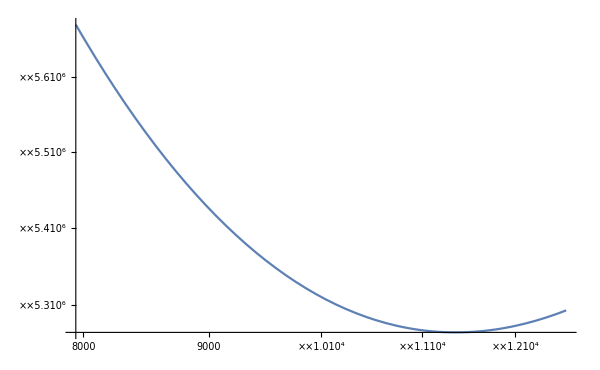

```mathematica
Plot[durmaxgauss[x],{x,10^3.9,10^4.1},ScalingFunctions->{"Log10","Log10"}]
```

General::munfl: Exp[-2.92963×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.9298×10^8] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

General::munfl: Exp[-2.92963×10^8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

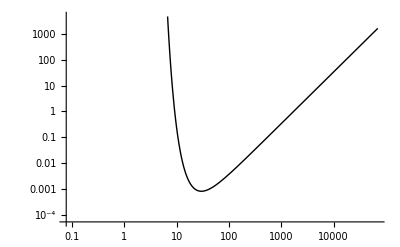

```mathematica
linesgauss=LogLogPlot[{durmaxgauss[x],maxdistgauss[x]},{x,10*Min[stats[[1;; , 1]]],10*Max[stats[[1;; ,1]]]},PlotRange->{{10*Min[stats[[1;; , 1]]],10*Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],Max[stats[[1;; ,2]]]*1000}},PlotStyle->Directive[Thick,Black]]
```

```mathematica
ListPointPlot3D[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic}]
```

-Graphics3D-

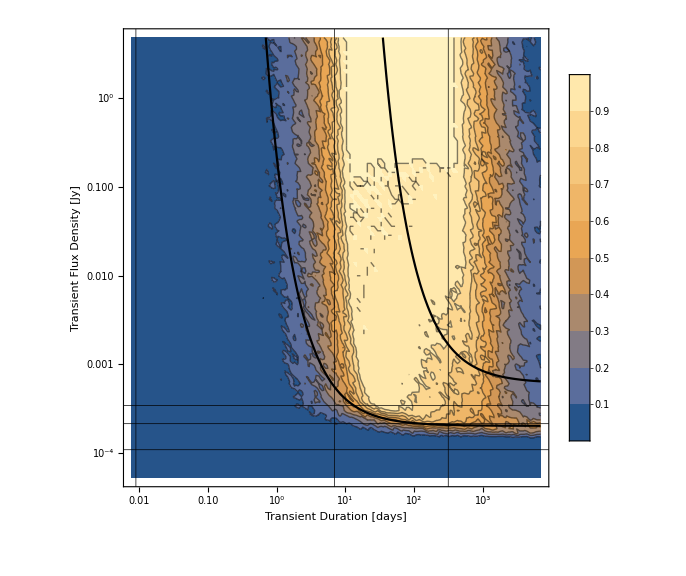

```mathematica
lines = Quiet[Plot[{durmaxfred[x],maxdistfred[x]},{x,Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},PlotRange->{{Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],Max[stats[[1;; ,2]]]}},PlotStyle->Directive[Thick,Black],ScalingFunctions->{"Log10","Log10"}]];
If[transientType =="tophat",ListContourPlot[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic},GridLines->gridlines,GridLinesStyle->Directive[Thick,Black],FrameLabel->{"Transient Duration [days]","Transient Flux Density [Jy]"},ImageSize->Large],ListContourPlot[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic},GridLines->gridlines,GridLinesStyle->Directive[Thick,Black],FrameLabel->{"Transient Duration [days]","Transient Flux Density [Jy]"},Epilog->lines[[1]],ImageSize->Large]]
```

```mathematica
(*Export["fred_lightcurve.pdf",%104]*)
```

```mathematica
-durmaxgauss[50]
```

-7.09322030989519×10^411

```mathematica
ftry1[x_]:=Max[obs[[1;; , 3]]]/(x-Max[gaps])*x
ftry2[x_]:=Max[obs[[1;; , 3]]]/(x-durmax)*x
ftry1[100]
```

0.00023229

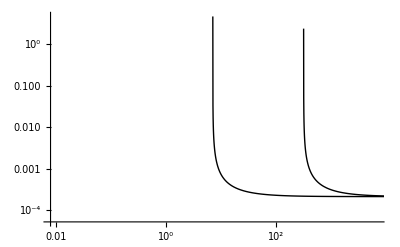

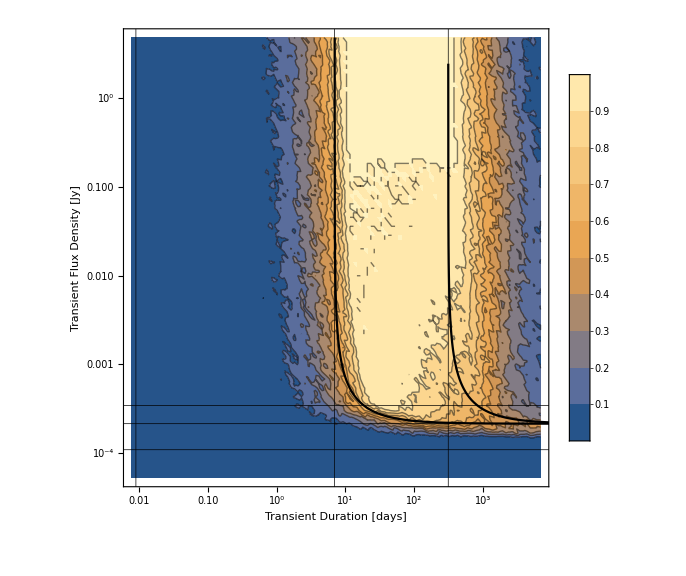

```mathematica
linesgauss=Quiet[Plot[{ftry1[x],ftry2[x]},{x,0.5,10^8},PlotRange->{{Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],Max[stats[[1;; ,2]]]}},PlotStyle->Directive[Thick,Black],ScalingFunctions->{"Log10","Log10"}]]
Show[ListContourPlot[stats[[1;;,1;;3]],PlotLegends->Automatic,ScalingFunctions->{"Log10","Log10",Automatic},GridLines->gridlines,GridLinesStyle->Directive[Thick,Black],FrameLabel->{"Transient Duration [days]","Transient Flux Density [Jy]"},ImageSize->Large,PlotRange->{{Min[stats[[1;; , 1]]],Max[stats[[1;; ,1]]]},{Min[stats[[1;; , 2]]],Max[stats[[1;; ,2]]]},{0,1.0}}],linesgauss]
```

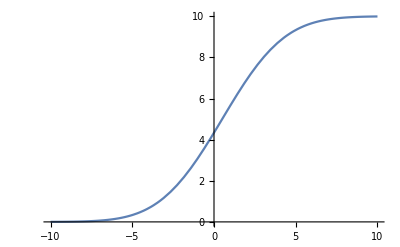

```mathematica
Plot[10*CDF[NormalDistribution[0+0.5, 0.5*6],x],{x,-10,10}]
```

```mathematica
obs[[1,1]]
```

18215.7

```mathematica
10*CDF[NormalDistribution[0+0.5, 0.5*6],8]-10*CDF[NormalDistribution[0+0.5, 0.5*6],4]
```

1.15463

```mathematica
Solve[ⅇ^-2*f/(√(2*π*τ^2))==f]
```

{{f→0},{τ→-1/(ⅇ^2 √(2 π))},{τ→1/(ⅇ^2 √(2 π))}}

```mathematica
ⅇ^-2*1/(√(2*π))
```

1/(ⅇ^2 √(2 π))

```mathematica
N[1/(ⅇ^2 √(2 π))]
```

0.053991

```mathematica
Integrate[F0*PDF[NormalDistribution[Tstart + τ/2,τ/6 ],t],t]
```

-1/2 F0 Erf[(3 (-2 t+2 Tstart+τ))/(√2 τ)]

```mathematica
CDF[NormalDistribution[Tstart + τ/2,τ/6 ],t]
```

1/2 Erfc[(3 √2 (-t+Tstart+τ/2))/τ]

```mathematica
CDF[NormalDistribution[μ,σ ],x]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

```mathematica
Series[A/(1/2 Erfc[(-x+μ1)/(√2 σ2)] -1/2 Erfc[(-x+μ2)/(√2 σ1)]),{x,0,1}]
```

(2 A)/(-Erfc[μ2/(√2 σ1)]+Erfc[μ1/(√2 σ2)])-(2 (A ⅇ^(-μ2^2/(2 σ1^2)-μ1^2/(2 σ2^2)) √(2/π) (ⅇ^(μ2^2/(2 σ1^2)) σ1-ⅇ^(μ1^2/(2 σ2^2)) σ2)) x)/(σ1 σ2 (Erfc[μ2/(√2 σ1)]-Erfc[μ1/(√2 σ2)])^2)+O[x]^2

```mathematica
Series[1/2 Erfc[(-x+μ1)/(√2 σ2)],{x,0,4}]
```

1/2 Erfc[μ1/(√2 σ2)]+(ⅇ^(-μ1^2/(2 σ2^2)) x)/(√(2 π) σ2)+(ⅇ^(-μ1^2/(2 σ2^2)) μ1 x^2)/(2 √(2 π) σ2^3)+(ⅇ^(-μ1^2/(2 σ2^2)) (μ1^2-σ2^2) x^3)/(6 √(2 π) σ2^5)+(ⅇ^(-μ1^2/(2 σ2^2)) μ1 (μ1^2-3 σ2^2) x^4)/(24 √(2 π) σ2^7)+O[x]^5